# Large-Amplitude Elongated-Body Theory of Fish Locomotion

## Borazjani and Sotiropoulos’ Carangiform Model

Two non-dimensional parameters that characterize the steady inline performance of a carangiform swimmer are the Reynolds number (Re) of the flow and the Strouhal number (St) of the undulatory body motion.
•L is the fish length
•U is the steady inline swimming speed
•v is the kinematic viscosity of the water
•A is the maximum lateral excursion of the tail over a cycle
•f is the tail beat frequency.
Most fishes have been shown swim near a ‘universal’ optimal value of 0.3.

### Fish body kinematics and non-dimensional parameters

The equation describing the lateral undulations of the fish body is given by

```mathematica
h[z_,t_]:=a[z]*Sin[k*z-ω*t]
```

where
•z is the axial (flow) direction measured along the fish axis from the tip of the fish head
•h(z,t) is the lateral excursion at time t
•a(z) is the first Fourier coefficient defining the amplitude envelope of lateral motion as a function of z
•k is the wave number of the body undulations that corresponds to a wavelength λ
•ω is the angular frequency
The values given below were experimentally determined by Videler and Hess.

```mathematica
Subscript[a, 0]=0.02
Subscript[a, 1]=-0.08
Subscript[a, 2]=0.16
Subscript[a, max]=0.1
Subscript[h, max]=0.1L
λ/L=0.95
```

```mathematica
Re=(L*U)/v;
St=2*f*Subscript[h, max];
a[z_]:=Subscript[a, 0]+Subscript[a, 1] z+Subscript[a, 2] z^2;
```

```mathematica
x[a_,t_]:=c*t*a;
(*z[a_,t_]:=d*t^2*a^3;*)
ρ=1;
s=1;
l=1;
k=(2*π)/(.95*l)
ω=(2*π*0.3)/(2*0.1)
t={0,0.1, 0.2, 0.3, 0.5,1,2,4,9,10,20}
```

SetDelayed::write: Tag List in {0,0.5 a c,a c,2 a c,4 a c,9 a c,10 a c,20 a c}[a_,t_] is Protected.

6.61388

9.42478

{0,0.1,0.2,0.3,0.5,1,2,4,9,10,20}

```mathematica
{0,0.1, 0.2, 0.3, 0.5,1,2,4,9,10,20}
```

{0,0.1,0.2,0.3,0.5,1,2,4,9,10,20}

```mathematica
Clear[z]
```

```mathematica
h[z_]=(0.002-0.08*z+0.16*z^2)*Sin[k*z-ω*t]
```

{(0.002-0.08 z+0.16 z^2) Sin[0.+6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[0.942478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[1.88496-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[2.82743-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[4.71239-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[9.42478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[18.8496-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[37.6991-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[84.823-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[94.2478-6.61388 z],-(0.002-0.08 z+0.16 z^2) Sin[188.496-6.61388 z]}

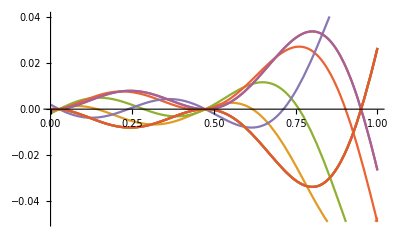

```mathematica
Plot[h,{z,0,1}]
```

Lighthill’s Elongated-Body Theory (EBT)

Lighthill’s elongated-body theory makes use of three principles:
	(i) Water momentum near a section of fish is in a direction perpendicular to the backbone and has magnitude equal to the virtual mass, m per unit length, times the component w of fish velocity in that direction.
	(ii) Thrust can be obtained by considering rate of change of momentum within a volume enclosing the fish whose boundary at each instant includes a flat surface Π perpendicular to the caudal fin through its posterior end.
	(iii) In the momentum balance it is necessary to take into account transfer of momentum across Π not only by convection but also by the action of the resultant 1/2 mw^2of the pressures generated by the motions within the plane Π.

```mathematica
u=D[x,t]*D[x,a]+D[z,t]*D[z,a]
w = D[z,t]*D[x,a]-D[x,t]*D[z,a]
```

```mathematica
m=1/4 π*ρ*s^2
```

```mathematica
{P1,Q1}=(m*w*{D[z,t],-D[x,t]}-1/2 m*w^2*{D[x,a],D[z,a]})
```

```mathematica
{P2, Q2}=D[Integrate[m*w*{-D[z,a],D[x,a]},{a,0,l}],t]
```

```mathematica
{P,Q}=({P1,Q1}/.a-> 0)-{P2, Q2}
```